```mathematica
spectralData={};
AppendTo[spectralData,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_04.dat","Table"]]];
AppendTo[spectralData,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_05.dat","Table"]]];
AppendTo[spectralData,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_06.dat","Table"]]];
AppendTo[spectralData,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_07.dat","Table"]]];
AppendTo[spectralData,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_08.dat","Table"]]];
AppendTo[spectralData,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_09.dat","Table"]]];
AppendTo[spectralData,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_10.dat","Table"]]];
```

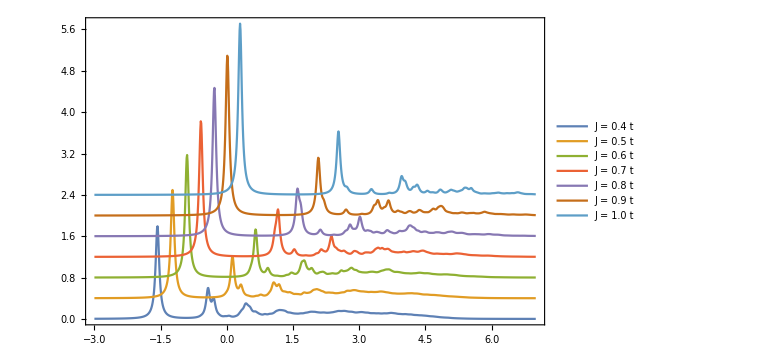

```mathematica
ListLinePlot[Table[spectralData[[it]]+0.4(it-1),{it,Length[spectralData]}],PlotRange->{{-3,7},All},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,(*PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},*)PlotLegends->{"J = 0.4 t","J = 0.5 t","J = 0.6 t","J = 0.7 t", "J = 0.8 t","J = 0.9 t","J = 1.0 t"}]
```

```mathematica
spectralData2={};
AppendTo[spectralData2,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_08.dat","Table"]]];
AppendTo[spectralData2,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_08_9.dat","Table"]]];
```

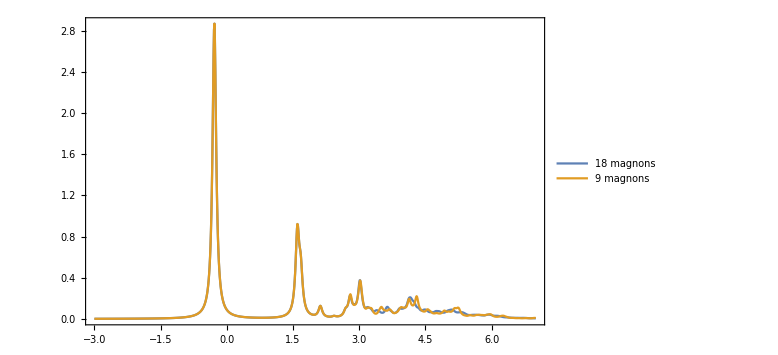

```mathematica
ListLinePlot[Table[spectralData2[[it]]+0.0(it-1),{it,Length[spectralData2]}],PlotRange->{{-3,7},All},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,(*PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},*)PlotLegends->{ "18 magnons", "9 magnons"}]
```

```mathematica
spectralData3={};
AppendTo[spectralData3,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_04.dat","Table"]]];
AppendTo[spectralData3,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_08.dat","Table"]]];
```

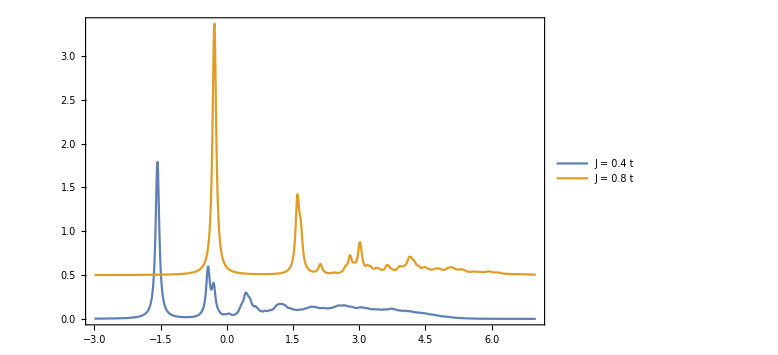

```mathematica
ListLinePlot[Table[spectralData3[[it]]+0.5(it-1),{it,Length[spectralData3]}],PlotRange->{{-3,7},All},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,(*PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},*)PlotLegends->{ "J = 0.4 t", "J = 0.8 t"}]
```

```mathematica
spectralData4={};
AppendTo[spectralData4,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_04.dat","Table"]]];
AppendTo[spectralData4,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_06.dat","Table"]]];
```

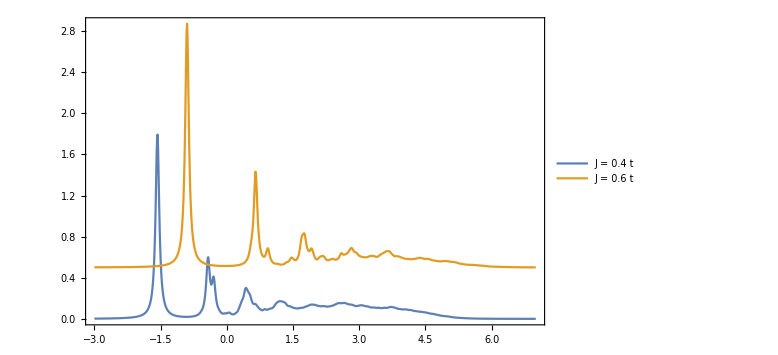

```mathematica
ListLinePlot[Table[spectralData4[[it]]+0.5(it-1),{it,Length[spectralData4]}],PlotRange->{{-3,7},All},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,(*PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},*)PlotLegends->{ "J = 0.4 t", "J = 0.6 t"}]
```

```mathematica
spectralData5={};
AppendTo[spectralData5,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_06.dat","Table"]]];
AppendTo[spectralData5,Flatten[Import["D:\\Dokumenty\\Materiały Naukowe\\Doktorat\\2D Square\\directGF\\bin\\spectral_06_10.dat","Table"]]];
```

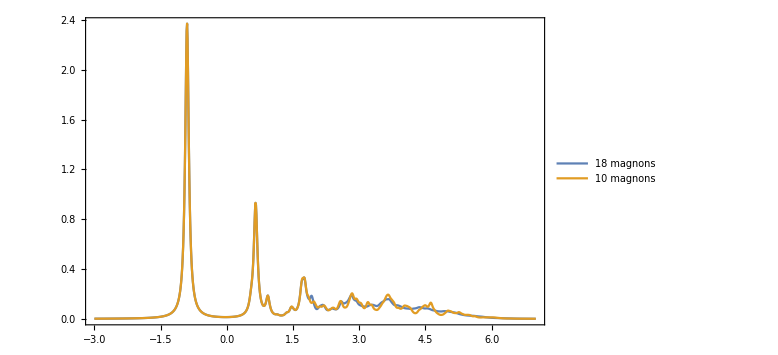

```mathematica
ListLinePlot[Table[spectralData5[[it]]+0.0(it-1),{it,Length[spectralData5]}],PlotRange->{{-3,7},All},DataRange->{-3,7},Frame->True,Axes->False,ImageSize->Large,(*PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},*)PlotLegends->{ "18 magnons", "10 magnons"}]
```